3

NDEigensystem::maxeigen: A maximum number of 47 eigenvalues and functions can be computed for this discretized system.

$Aborted

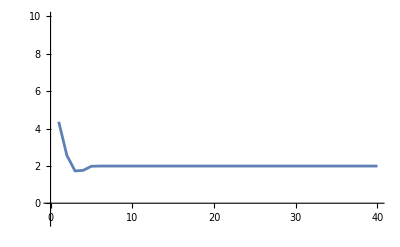

```mathematica
Remove["Global`*"]
ℋ[α_,β_,Δ_,ml_]:=-1/2(ψ''[r]+1/r ψ'[r]-ml^2/r^2 ψ[r])+1/2 α*r^2*ψ[r]+β*r^4*ψ[r]-Δ*ml*ψ[r]
numstates :=50;
α:=.05
ω0:=1I
Δ:=0
rmin:=1; rmax:=25;
steps:=100
dr:=(rmax-rmin)/steps
energies:={}
state=3
Monitor[For[rint=rmin,rint<=rmax, rint=rint+dr,
	lim =If[α!=0, rint √((Abs[ω0^2]+Δ^2)/(4*α)),2*rint];
	{vals, funcs} =NDEigensystem[{ℋ[ω0^2+Δ^2,α,Δ,0]},ψ,{r,0,lim},numstates,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->.1}}}];
	data={vals,funcs};
	data=data[[All,Ordering@First@data]];
	p=Plot[data[[2]][[state]][r],{r,0,25},PlotRange->{-1,1}];
	AppendTo[energies,data[[1]][[state]]]
],{rint,data[[1]][[state]],p}]
ListLinePlot[energies,PlotRange->{-1,10}]
```

2D

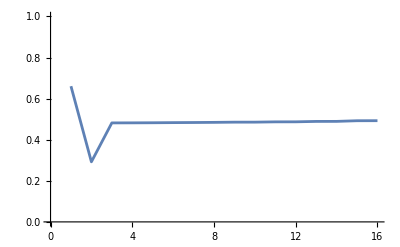

```mathematica
Remove["Global`*"]
ℋ[α_,β_,Δ_]:=-1/2 Laplacian[ψ[r,θ],{r,θ},"Polar"]+1/2 α*r^2*ψ[r,θ]+β*r^4*ψ[r,θ]+I*Δ*D[ψ[r,θ],θ]
numstates :=50
α:=.05
ω0:=1I
Δ:=0
minr:=1; maxr:=10;
steps:=15
dr:=(maxr-minr)/steps
energies:={}
state:=6
Monitor[For[rint=minr,rint<=maxr, rint=rint+dr,
	lim:=If[α!=0,rint √((Abs[ω0^2]+Δ^2)/(4*α)),2*rint];
	{vals,funcs}=NDEigensystem[{ℋ[ω0^2+Δ^2,α,Δ],ψ[r,0]==ψ[r,2π]},
	ψ,{r,0,lim},{θ,0,2π},numstates,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->Automatic}}}];
	data ={vals,funcs};
	data=data[[All,Ordering@First@data]];
	p=ParametricPlot3D[{r*Cos[θ],r*Sin[θ],Abs[data[[2]][[state]][r,θ]]},{r,0,3*√((Abs[ω0^2]+Δ^2)/(4*α))},{θ,0,2π},
					PlotRange->{{-3*√((Abs[ω0^2]+Δ^2)/(4*α)), 3*√((Abs[ω0^2]+Δ^2)/(4*α))},{-3*√((Abs[ω0^2]+Δ^2)/(4*α)),3*√((Abs[ω0^2]+Δ^2)/(4*α))},{0,.75}},
					BoxRatios->{1,1,1}];
	AppendTo[energies,data[[1]][[state]]]
],{rint,data[[1]][[state]],p}]
ListLinePlot[Abs[energies],PlotRange->{0,1}]
```

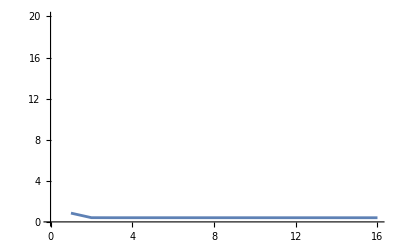

-Graphics3D-

```mathematica
ListLinePlot[Abs[energies],PlotRange->{0,20}]
ParametricPlot3D[{r*Cos[θ],r*Sin[θ],Abs[data[[2]][[4]][r,θ]]},{r,0,lim},{θ,0,2π},PlotRange->5]
```